```mathematica
Lecture 6:Modules, Recursion
```

## Modules and local variables

### Exercise Subsection

What does the following cell do when evaluated?

```mathematica
n=6;
Module[{k=4,j=0},
n=n+k;
Range@15;
n^2]
{n,k,j}
```

100

{10,k,j}

### Exercise Subsection

What does the following cell do when evaluated?

```mathematica
f[L_List]:=Module[{A=L/.{x_/;Positive@x->1,x_/;Negative@x->-1}},
FreeQ[A,{___,1,1,___}]&&FreeQ[A,{___,-1,-1,___}]]
```

```mathematica
f[{1,-2,3}]
```

True

This command defines a function f which has input a list L and outputs True if L never has two consecutive positive numbers or negative numbers and False otherwise.

```mathematica
f[n_]:=Module[{k=n},While[k<100,k=k+1];k]
```

```mathematica
f[5]
```

100

## Recursions

### Exercise Subsection

What does the following cell do when evaluated?

```mathematica
f[n_]:=Which[n==0,1,n==1,1,True,f[n-1]+f[n-2]]
f/@Range@10
```

{1,2,3,5,8,13,21,34,55,89}

### Exercise Subsection

What does the following cell do when evaluated?

```mathematica
f[n_Integer/;n>=0]:=If[n<=1,1,n f[n-1]]
f/@Range@10
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

### Exercise Subsection

Recall from Exercise Set 5 that a Gray code (see https://en.wikipedia.org/wiki/Gray_code ) is an ordering of all bit strings (which are lists with elements either 0 or 1) such that consecutive bit strings differ in exactly one position.  Using the idea outlined in Set 5, we can recursively define a gray code; see this example:

```mathematica
GrayCode[n_]:=If[n==0,{{}},Join[Prepend[#,0]&/@GrayCode[n-1],Prepend[#,1]&/@Reverse@GrayCode[n-1]]]
```

```mathematica
GrayCode@3
```

{{0,0,0},{0,0,1},{0,1,1},{0,1,0},{1,1,0},{1,1,1},{1,0,1},{1,0,0}}

### Exercise Subsection

The Euclidean algorithm finds the greatest common divisor of a and b recursively.  Write down the values iteratively taken by a and b in the recursion below when starting with a=13 and b=21.

```mathematica
Euclidean[a_,b_]:=If[b==0,a,Print[{a,b}];Euclidean[b,Mod[a,b]]]
```

### Exercise Subsection

Define a recursive function named MergeLists[L1_,L2_,L3_:{}] that takes in three lists L1, L2, and L3 (as an optional argument that defaults to {}) of nondecreasing numbers and outputs the sorted list with the numbers found in L1 and L2. The function should do the following:

1. Find the smaller of the two first elements in L1 and L2, say s.
2. Remove s from L1 (or L2) and append s to L3.
2. Repeat until both L1 and L2 are empty, then return L3.

No built-in sorting operations can be used to do this exercise.

```mathematica
MergeLists[L1_,L2_,L3_:{}]:=Which[
L1=={}||L2=={},Join[L3,L1,L2],
First@L1<=First@L2,MergeLists[Rest@L1,L2,Join[L3,{First@L1}]],
True,MergeLists[L2,L1,L3]]
```

### Exercise Subsection

Merge sort (see https://en.wikipedia.org/wiki/Merge_sort ) is is a divide and conquer algorithm for sorting a list of numbers.  It works on the list L by 

1. Returning L in the case when L contains only one element, 
2. Merging (using the MergeLists function defined in the previous exercise) the list L[[;;1]] of length 1 containing only the first element on L and the Mergesort -ed list L[[2;;]].

Create a recursive function called Mergesort[L_List] that takes a list L as an input and returns the list in nondecreasing order.  You may not use any built-in sorting operations.

```mathematica
MergeSort[L_List]:=If[Length@L<=1,L,MergeLists[{First@L},MergeSort[Rest@L]]]
```

```mathematica
MergeSort[{3,1,1,4,11,5,5,2}]
```

{1,1,2,3,4,5,5,11}

## Memoization

### Exercise Subsection

The Pell numbers are defined by P_0=0, P_1= 1 and P_n= 2 P_(n-1)+P_(n-2) for n ≥ 2.  Write a recursive function Pell that returns P_n and then verify that

P_n= ((1 + √2)^n- (1 - √2)^n)/(2 √2)

holds for 0 ≤n ≤ 100.  The function Pell should take advantage of memoization.

```mathematica
Clear[Pell]
Pell[n_]:=Pell[n]=If[n<=1,n,2 Pell[n-1]+Pell[n-2]]
```

```mathematica
Timing[Pell[500]]
```

{0.002021,86357025589181651134620667861013069415399299912892782644299662477978048037564799544047425062310179523844369817367212413811972726519467358466915523378127385972351411363620519115519305266827228}

### Exercise Subsection

The Catalan sequence (see https://en.wikipedia.org/wiki/Catalan_number ) is defined such that c[0] = 1 and c[n] is equal to the sum 

c[0] c[n-1] + c[1] c[n-2] + ... + c[n-1] c[0]

Using Timing to find the 15th Catalan number c[15] without using memoization and then compare Timing to find c[15] when implementing memoization.

```mathematica
Clear[Cat]
Cat[n_]:=Cat[n]=If[n==0,1,Sum[Cat[i] Cat[n-1-i],{i,0,n-1}]]
```

### Exercise Subsection

The Yellowstone sequence is the sequence y[n] with y[1] = 1, y[2] = 2, y[3] = 3, and then y[n] is the smallest number not already on the list such that the greatest common divisor (the GCD) of y[n] and y[n-1] is 1 and the greatest common divisor of y[n] and y[n-2] is not 1.   Define this sequence recursively, taking advantage of memoization.   Then Map y to the first 100  positive integers.

```mathematica
Clear[y]
y[n_]:=y[n]=If[n<=3,n,Module[{k=1},While[MemberQ[y/@Range[n-1],k]||GCD[k,y[n-1]]!=1||GCD[k,y[n-2]]==1,k=k+1];
k]]
```

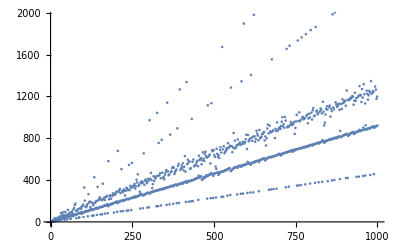

```mathematica
y/@Range@1000//ListPlot
```

### Exercise Subsection

Using memoization, define a sequence a[n] such that a[1]=1 and otherwise a[n+1] is equal to a[n]/n if this is an integer and n a[n] otherwise. What is a[100]?

### Exercise Subsection

Suppose f[n] is a function such that f[1]=1 and f[2 n] = f[n] and f[2n+1] = f[2n] + 1 for all positive integers n.  Find the first value of n for which f[n] = 10.

### Exercise Subsection

The Hénon map, see (https://en.wikipedia.org/wiki/H%C3%A9non_map ) is a pair of sequences x[n] and y[n] defined by x[0]=1, y[0]=1, x[n]=1-1.4 x[n-1]^2 + y[n-1] , and y[n] = 0.3 x[n-1].

Find the list of pairs {x[n],y[n]} for n = 0, 1,...,10000, and then use the command ListPlot on this set of pairs to visualize them in the plane.

```mathematica
Clear[x,y]
x[n_]:=x[n]=If[n==0,1,1-1.4 x[n-1]^2 + y[n-1]]
y[n_]:=y[n]=If[n==0,1,.3 x[n-1]]
```